# Mathematica Standalone Example 22

## Sequential Analysis

A batch ray trace is run in a sequential sample file. A list of 315 rays is generated and passed to ZOS-API for tracing in a single operation. This greatly reduces overhead when tracing a large number of rays. Resulting ray data is stored and displayed outside of OpticStudio. Using the native OpticStudio spot diagram analysis, geometric and RMS spot radius are retrieved, and are also displayed.

## 1. Set up the interface

### Install Mathematica’s NETLink context

```mathematica
Needs["NETLink`"]
```

### Set a default directory and define the path to the ZOS-API libraries

```mathematica
LoadNETType["Microsoft.Win32.Registry"];
zemaxData = Registry`GetValue["HKEY_CURRENT_USER\\Software\\Zemax", "ZemaxRoot", -1];
samplesDir=FileNameJoin[{zemaxData, "\\Samples"}];
```

### Initialize the connection

```mathematica
netHelper = FileNameJoin[{zemaxData, "\\ZOS-API\\Libraries\\ZOSAPI_NetHelper.dll"}];
LoadNETAssembly[netHelper];

LoadNETType["ZOSAPI_NetHelper.ZOSAPI_Initializer"];
success = ZOSAPIUInitializer`Initialize[];
(*Note -- uncomment the following line to use a custom initialization path*)
(*success = ZOSAPIUInitializer`Initialize["C:\\Program Files\\OpticStudio"];*)
```

```mathematica
If[success == True,{
found="Found OpticStudio at: ";
location=ToString[ZOSAPIUInitializer`GetZemaxDirectory[]];
found<>location
}, "Failed to connect!"]
```

{Found OpticStudio at: c:\program files\zemax opticstudio 21.3.1}

### Load assemblies

```mathematica
zosapi=LoadNETAssembly[FileNameJoin[{location, "\\ZOSAPI.dll"}]];
interfaces=LoadNETAssembly[FileNameJoin[{location, "\\ZOSAPI_Interfaces.dll"}]];
```

### Open connection and create the application

```mathematica
(*Open connection and create an application*)
theConnection=NETNew["ZOSAPI.ZOSAPI_Connection"];
theApplication=theConnection@CreateNewApplication[];
```

### Perform final checks regarding the connection

```mathematica
(*Check that a connection was established*)
If[NETObjectQ[theApplication] == False, "An unknown connection error occurred!", "";]
(*Check license status*)
If[theApplication@IsValidLicenseForAPI== False, {
theApplication@CloseApplication[];
"License check failed!"}, ""];
```

## 2. Import Modules

### Module to view the LDE information

```mathematica
displayLDE:=Module[{numberofsurfaces,LDEdata,tempsurf},
numberofsurfaces=theLDE@NumberOfSurfaces;
LDEdata = Table[,{a,1,numberofsurfaces},{b,1,9}];
Do[
tempsurf = theLDE@GetSurfaceAt[j];
LDEdata[[j+1,1]]=tempsurf@SurfaceNumber;
LDEdata[[j+1,2]]=tempsurf@Type@ToString[""];
LDEdata[[j+1,3]]=tempsurf@Comment;
LDEdata[[j+1,4]]=tempsurf@Radius;
LDEdata[[j+1,5]]=tempsurf@Conic;
LDEdata[[j+1,6]]=tempsurf@Thickness;
LDEdata[[j+1,7]]=tempsurf@Material;
LDEdata[[j+1,8]]=tempsurf@Coating;
LDEdata[[j+1,9]]=tempsurf@SemiDiameter
,{j,0,numberofsurfaces-1,1}];
TableForm[LDEdata,TableHeadings->{None,{"surface #","surface type","comment","ROC","conic","thickness","material","coating","semi-diameter"}}]
]
```

## 3. Open file and set up Batch Ray Trace

### Generate a Mathematica API folder

```mathematica
apiDir=FileNameJoin[{samplesDir, "\\API\\Mathematica"}];
If[DirectoryQ[apiDir]==False, CreateDirectory[apiDir]]
```

### Set up primary optical system and open file

```mathematica
LoadNETType["ZOSAPI.SystemType"];
```

```mathematica
theSystem = theApplication@CreateNewSystem[SystemType`Sequential];
```

```mathematica
(*Open a sample file*)
testFile = FileNameJoin[{samplesDir, "\\Sequential\\Objectives\\Double Gauss 28 degree field.zmx"}];
theSystem@LoadFile[testFile, False];
```

```mathematica
(*Pull surfaces into API*)
theLDE = theSystem@LDE;
```

```mathematica
displayLDE
```

surface # | surface type | comment | ROC | conic | thickness | material | coating | semi-diameter
0 | Standard |  | ∞ | 0. | ∞ |  |  | ∞
1 | Standard |  | 54.1532 | 0. | 8.74666 | SK2 | AR | 29.2253
2 | Standard |  | 152.522 | 0. | 0.5 |  | AR | 28.141
3 | Standard |  | 35.9506 | 0. | 14. | SK16 | AR | 24.2958
4 | Standard |  | ∞ | 0. | 3.77697 | F5 |  | 21.2972
5 | Standard |  | 22.2699 | 0. | 14.2531 |  | AR | 14.9194
6 | Standard |  | ∞ | 0. | 12.4281 |  |  | 10.2288
7 | Standard |  | -25.685 | 0. | 3.77697 | F5 | AR | 13.1878
8 | Standard |  | ∞ | 0. | 10.8339 | SK16 |  | 16.4681
9 | Standard |  | -36.9802 | 0. | 0.5 |  | AR | 18.9296
10 | Standard |  | 196.417 | 0. | 6.85817 | SK16 | AR | 21.3108
11 | Standard |  | -67.1476 | 0. | 57.3145 |  | AR | 21.6463
12 | Standard |  | ∞ | 0. | ∞ |  |  | 24.5705

### Open Batch Ray Trace and set up the analysis

```mathematica
(*Open Batch Ray Trace and load enumuerators we will need*)
raytrace = theSystem@Tools@OpenBatchRayTrace[];
LoadNETType["ZOSAPI.Tools.RayTrace.RaysType"];
LoadNETType["ZOSAPI.Tools.RayTrace.OPDMode"];
```

```mathematica
(*Define constants for the ray trace*)
(*We want general information about the system such as number of surfaces, number wavelengths, number fields, max field*)
(*In addition, we also want to declare the field X and Y normalization values. In this file, there are only Y-fields so hx == 0 and hy will be populated with the normalization values*)
nsur = theSystem@LDE@NumberOfSurfaces;
maxRays = 30;
normUnPolData=raytrace@CreateNormUnpol[((maxRays + 1) (maxRays + 1)), RaysType`Real, nsur];
```

```mathematica
hx = 0;
maxWave = theSystem@SystemData@Wavelengths@NumberOfWavelengths;
numFields = theSystem@SystemData@Fields@NumberOfFields;
fieldArray = Table[theSystem@SystemData@Fields@GetField[i]@Y, {i, 1, numFields}];
maxField = Max[fieldArray];
hyArray = Table[fieldArray[[i]]/maxField, {i, 1, numFields}]
```

{0.,0.714286,1.}

```mathematica
(*Declare arrays to hold x/y image plane data*)
numFields = theSystem@SystemData@Fields@NumberOfFields;
xAry = Table[0, numFields, maxWave, ((maxRays + 1) (maxRays+1))];
yAry = Table[0, numFields, maxWave, ((maxRays + 1) (maxRays+1))];
(*xAry = Table[0, numFields, maxWave, 10];
yAry = Table[0, numFields, maxWave, 10];*)
```

## 4. Run the Batch Ray Trace and plot the values

### Run the Batch Ray Trace, storing data to our X and Y arrays

```mathematica
(*Define the commands for pulling the ray results. We will use this later*)
successNextResult:=normUnPolData@ReadNextResult[rayNumber, errCode, vigCode, x, y, dummyVal, dummyVal, dummyVal, dummyVal, dummyVal, dummyVal, dummyVal, dummyVal, dummyVal];
```

```mathematica
For[field = 1, field ≤ numFields, field++, 
For[wave = 1, wave≤ maxWave, wave++, 
normUnPolData@ClearData[];
waveNumber = wave;
For[ray = 1, ray≤((maxRays+1) (maxRays+1)), ray++, 
px = RandomReal[]*2 - 1;
py = RandomReal[]*2 - 1;
While[(px^2+py^2 > 1), py= RandomReal[]*2 - 1];
normUnPolData@AddRay[waveNumber, hx, hyArray[[field]], px, py, OPDMode`None];
];
raytrace@RunAndWaitForCompletion[];

(*Begin reading results. We can utilize the already-built field and wave loops for this*)
normUnPolData@StartReadingResults[];
While[successNextResult==True, {
If[((errCode==0)&&(vigCode==0)),
xAry[[field, wave, rayNumber]]=x;
yAry[[field, wave, rayNumber]]=y]
}];
]
]
```

```mathematica
(*Close the tool*)
raytrace@Close[];
```

### Plot the data

```mathematica
(*Create an array to hold combined {x,y} data*)
```

```mathematica
fullDataSet=Table[0,3,3];
```

```mathematica
For[field = 1, field≤ numFields, field++,
For[wave=1, wave≤ maxWave, wave++,
thatArrayTho=Partition[Riffle[Flatten[xAry[[field, wave]]], Flatten[yAry[[field,wave]]]], 2];
fullDataSet[[field, wave]]=thatArrayTho
];
]
```

```mathematica
field1 = ListPlot[{fullDataSet[[1,1]], fullDataSet[[1,2]], fullDataSet[[1,3]]}, ColorFunction->{Blue, Green, Red}, PlotLabel-> "Field 1"];
field2 = ListPlot[{fullDataSet[[2,1]], fullDataSet[[2,2]], fullDataSet[[2,3]]}, ColorFunction->{Blue, Green, Red}, PlotLabel-> "Field 2"];
field3=ListPlot[{fullDataSet[[3,1]], fullDataSet[[3,2]], fullDataSet[[3,3]]}, ColorFunction->{Blue, Green, Red}, PlotLabel->"Field 3"];
```

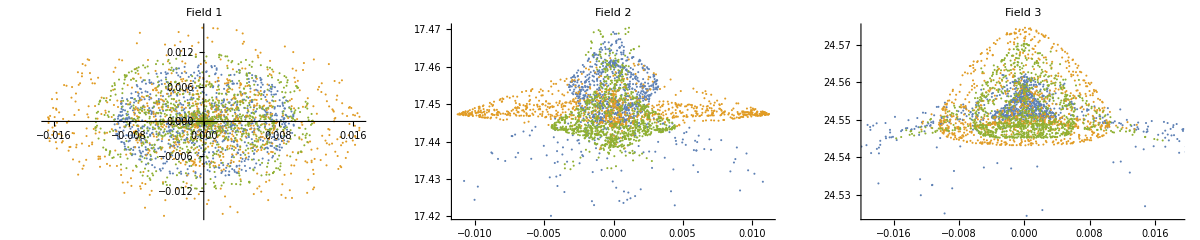

```mathematica
GraphicsRow[{field1, field2, field3}, ImageSize->Full]
```

### Compare these results with the numeric output of the Spot Diagram

```mathematica
LoadNETType["ZOSAPI.Analysis.AnalysisIDM"];
LoadNETType["ZOSAPI.Analysis.Settings.Spot.Reference"];
```

```mathematica
(*Open the Spot Diagram and apply our settings*)
spot=theSystem@Analyses@NewUAnalysis[AnalysisIDM`StandardSpot];
spotSettings = spot@GetSettings[];
spotSettings@Field@SetFieldNumber[0];
spotSettings@Wavelength@SetWavelengthNumber[0];
spotSettings@ReferTo=Reference`Centroid;
```

```mathematica
spot@ApplyAndWaitForCompletion[];
spotResults = spot@GetResults[];
```

```mathematica
Print["RMS radius: ", spotResults@SpotData@GetRMSSpotSizeFor[1,1], " ", spotResults@SpotData@GetRMSSpotSizeFor[2,1], " ", spotResults@SpotData@GetRMSSpotSizeFor[3,1]]
Print["GEO radius: ", spotResults@SpotData@GetGeoSpotSizeFor[1,1], " ", spotResults@SpotData@GetGeoSpotSizeFor[2,1], " ", spotResults@SpotData@GetGeoSpotSizeFor[3,1]]
```

RMS radius: 8.50062 9.35326 11.4963

GEO radius: 16.8724 29.9885 38.2143

## Close the application

```mathematica
theApplication@CloseApplication[];
```